```mathematica
(* Convert a colour RGB image to grayscale *)
```

```mathematica
(* Since RGB images are composed of red green and blue channels, averaging these pixel values will give us a single pixel value which can be used as grayscale *)
```

```mathematica
(* TEST - create an average image of a 1D image  *)
```

```mathematica
(* define the image as a 1D array of pixel values between 0 and 255 *)
```

```mathematica
colours=Table[
{RandomReal[1],RandomReal[1],RandomReal[1]},{10}
]
```

{{0.946817,0.194567,0.493144},{0.656066,0.0619158,0.505979},{0.60832,0.020667,0.631014},{0.54909,0.00818998,0.141107},{0.0935201,0.64175,0.533029},{0.321566,0.566463,0.481427},{0.83097,0.302915,0.554459},{0.425679,0.157365,0.0859321},{0.154577,0.433958,0.471096},{0.850965,0.602461,0.0938325}}

```mathematica
(* define a delayed function which calculates the average RGB values per pixel *)
```

```mathematica
average[list_]:=Total[list/3];
```

```mathematica
(* average teh pixel values in the colour vector *)
```

```mathematica
averaged=Table[
average[colours[[n]]],{n,1,Length[colours]}
]
```

{0.596026,0.655416,0.439814,0.64232,0.741016,0.87444,0.15657,0.392406,0.481529,0.62921}

```mathematica
(* Compare original with averaged values  *)
```

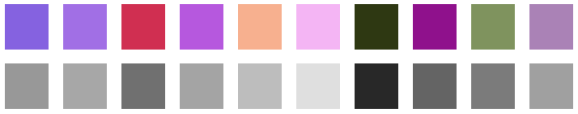

```mathematica
GraphicsGrid[{
Table[
Graphics[{RGBColor[colours[[n]]],Rectangle[]}]
,{n,1,Length[colours]}
],
Table[
Graphics[{GrayLevel[averaged[[n]]],Rectangle[]}]
,{n,1,Length[colours]}
]
}]
```

```mathematica
(* sample image *)
```

```mathematica
sun=-Graphics-;
```

```mathematica
ImageDimensions[sun]
```

{259,194}

```mathematica
(* Average each row in the image *)
```

```mathematica
averaged=Table[
Table[
average[ImageData[sun][[row, column]]],{column,1,259}
],{row,1,194}
];
```

```mathematica
Image[averaged]
```

-Graphics-